```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
(*For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];

];

];
{kglob,fglob}
]
```

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},
(*psis=GeneratePsis[order];*)
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};
];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
{psis,GradPhi,Jac,x,y}
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
fu=-1;
For[i=1,i≤ nnodes,i++,

ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order 4];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];
Print["elcoords = ",elcoords];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,topol_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];

(*nnodes=Length[allcoords] order;*)
sz= Length[nnodes]2;
Print["Nnodes = ",nnodes];
Print["Length[nnodes] = ",Length[nnodes]];
Print["sz= ",sz];
rows=order 4;
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;

{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineNewman[EF_,fx_,order_,nodes_,topol_,id1_,id2_,fxorfy_]:=Block[{Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,vecnodes,iel,vecids={},id={}},
iel=Length[topol];
vecnodes={};
For[j=1,j≤iel,j++,
node={};
id={};
For[i=1,i≤order 4,i++,
(*Print["j = ",j];
Print["i = ",i];
Print["topol[[j,i]] = ",topol[[j,i]]];
Print["nodes[[ topol[[j,i]] ]]= ",nodes[[ topol[[j,i]] ]]];*)
If[nodes[[ topol[[j,i]] ]][[2]]==nodes[[id1]][[2]],
AppendTo[node,nodes[[ topol[[j,i]] ]]];
AppendTo[id,topol[[j,i]]];
];
];
If[Length[node]≠0,
node=SortBy[node,Small];
AppendTo[vecnodes,node];
(*id=SortBy[id,Small];
AppendTo[vecids,id];*)
Print["aid = ",id];
If[order==1,
id=Sort[id,Greater];
];
If[order==2,
id=Sort[id];
id=Sort[id,Greater];
];
Print["did = ",id];
AppendTo[vecids,id];
];
];
Print["vecnodes = ",vecnodes];
Print["vecids = ",vecids];
el=Length[vecnodes];

{elsw,ids}=DefineLineNodes[id1,id2,nodes];
fi=1;
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];

co=vecnodes[[i]];
Print["co = ",co];

newco=co;
xx=Sum[shapes[[i]] newco[[i]][[1]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Print["vecids[[i]]= ",vecids[[i]]];
Print["integralxi1= ",integralxi1];
If[fxorfy==1,(*fy*)

If[order==1,
Ef[[ vecids[[i,1]] 2]]+=integralxi1[[1]];
Ef[[ vecids[[i,2]] 2]]+=integralxi1[[2]];
];
If[order==2,
(*Print["vecids[[i]]= ",vecids[[i]]];
Print["vecids[[i,2]] = ",vecids[[i,2]]];
Print["vecids[[i,3]] = ",vecids[[i,3]]];
Print["vecids[[i,3]] = ",vecids[[i,3]]];
Print["co[[1]] = ",co[[1]]];
Print["co[[2]] = ",co[[2]]];
Print["co[[3]] = ",co[[3]]];*)
Print["vecids[[i,1]] 2 = ",vecids[[i,1]] 2];
Print["vecids[[i,2]] 2 = ",vecids[[i,2]] 2];
Print["vecids[[i,3]] 2 = ",vecids[[i,3]] 2];

Print["vecids[[i,1]]  = ",vecids[[i,1]] ];

Ef[[vecids[[i,1]] 2]]+=integralxi1[[1]];
Ef[[ vecids[[i,2]] 2]]+=integralxi1[[2]];
Ef[[ vecids[[i,3]] 2]]+=integralxi1[[3]];
];
,
(*fx*)
Ef[[ ids[[i]]2-1 ]]+=integralxi1[[1]];
Ef[[ ids[[i]]2 ]]+=integralxi1[[2]];
];
];
Ef
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_]:=Block[{nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac},
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};
];
nels=Length[topol];
sol=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

For[j=1,j≤4 order,j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
];

For[j=1,j≤4 order,j++,
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] DetJac);
sol[[i,2]]+=(psis[[j]] coefs[[2id]] DetJac);

(*duxdx*)
dsol[[i,1]]+=(D[psis[[j]],xi] coefs[[2 id-1]] DetJac);
(*duxdy*)
dsol[[i,2]]+=(D[psis[[j]],eta] coefs[[2id-1]] DetJac);
(*duydx*)
dsol[[i,3]]+=(D[psis[[j]],xi] coefs[[2id]] DetJac);
(*duydy*)
dsol[[i,4]]+=(D[psis[[j]],eta] coefs[[2id]] DetJac);
(*Print["j+k = ",j+k];
Print["j = ",j];*)
];

];
{sol,dsol}
]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

eps=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.{ex,ey,exy};
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,eps}
];
```

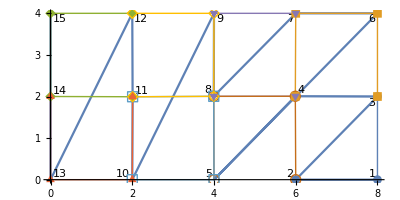

Nnodes = {{8,0},{6,0},{8,2},{5.98992,2.0057},{4,0},{8,4},{6,4},{3.99376,2.00386},{4,4},{2,0},{2.00848,1.99398},{2,4},{0,0},{0,2},{0,4}}

Length[nnodes] = 15

sz= 30

aid = {6,7}

did = {7,6}

aid = {12,15}

did = {15,12}

aid = {7,9}

did = {9,7}

aid = {9,12}

did = {12,9}

vecnodes = {{{6,4},{8,4}},{{0,4},{2,4}},{{4,4},{6,4}},{{2,4},{4,4}}}

vecids = {{7,6},{15,12},{9,7},{12,9}}

co = {{6,4},{8,4}}

vecids[[i]]= {7,6}

integralxi1= {-96.1776,-98.7215}

co = {{0,4},{2,4}}

vecids[[i]]= {15,12}

integralxi1= {-12.9894,-25.7784}

co = {{4,4},{6,4}}

vecids[[i]]= {9,7}

integralxi1= {-78.9915,-86.2359}

co = {{2,4},{4,4}}

vecids[[i]]= {12,9}

integralxi1= {-49.7797,-60.6217}

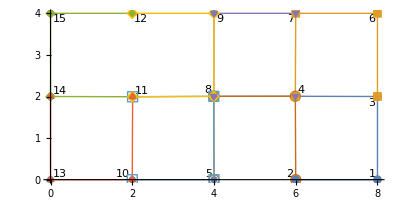

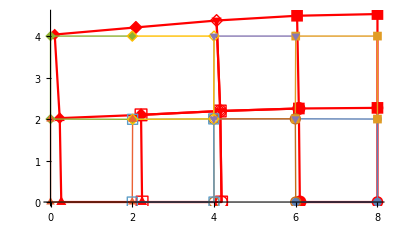

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidels-ex1-p1.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidnodes-ex1-p1.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListLinePlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,13,1,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,6,{{10^12,1},{1,1}},{0,0}];

q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=-ContributeLineNewman[FE,f,order,nnodes,topol,15,6,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Banded"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]




defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
sol//Chop
```

{0,0,2.52827×10^-6,0,0,6.7362×10^-6,2.16096×10^-6,6.22531×10^-6,4.63127×10^-6,0,0,0.0000132707,8.21322×10^-7,0.000012252,3.97182×10^-6,4.74779×10^-6,1.57456×10^-6,9.37919×10^-6,6.00761×10^-6,0,5.15634×10^-6,2.67894×10^-6,2.21019×10^-6,5.21949×10^-6,6.5766×10^-6,0,5.62525×10^-6,5.50859×10^-7,2.54474×10^-6,9.34056×10^-7}

```mathematica
topol
```

{{2,1,3,4},{3,6,7,4},{12,15,14,11},{14,13,10,11},{7,9,8,4},{2,4,8,5},{10,5,8,11},{11,8,9,12}}

```mathematica
nnodes
```

{{8,0},{6,0},{8,2},{5.98992,2.0057},{4,0},{8,4},{6,4},{3.99376,2.00386},{4,4},{2,0},{2.00848,1.99398},{2,4},{0,0},{0,2},{0,4}}

```mathematica
allcoords
```

{{{6,0},{8,0},{8,2},{5.98992,2.0057}},{{8,2},{8,4},{6,4},{5.98992,2.0057}},{{2,4},{0,4},{0,2},{2.00848,1.99398}},{{0,2},{0,0},{2,0},{2.00848,1.99398}},{{6,4},{4,4},{3.99376,2.00386},{5.98992,2.0057}},{{6,0},{5.98992,2.0057},{3.99376,2.00386},{4,0}},{{2,0},{4,0},{3.99376,2.00386},{2.00848,1.99398}},{{2.00848,1.99398},{3.99376,2.00386},{4,4},{2,4}}}

```mathematica
topol
```

{{2,1,3,4},{3,6,7,4},{12,15,14,11},{14,13,10,11},{7,9,8,4},{2,4,8,5},{10,5,8,11},{11,8,9,12}}

```mathematica
sol[[14 2-1]]
```

5.62525×10^-6

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2}}

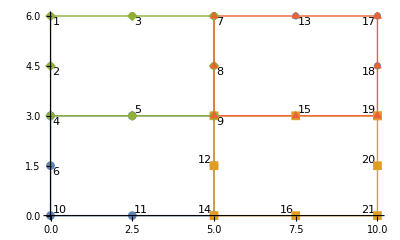

Nnodes = {{0,6},{0,4.5},{2.5,6},{0,3},{2.5,3},{0,1.5},{5,6},{5,4.5},{5,3},{0,0},{2.5,0},{5,1.5},{7.5,6},{5,0},{7.5,3},{7.5,0},{10,6},{10,4.5},{10,3},{10,1.5},{10,0}}

Length[nnodes] = 21

sz= 42

42

KE = (1.22151×10^19 | -6.33508×10^6 | -1.72355×10^7 | 8.50382×10^6 | 4.85039×10^6 | -2.02179×10^6 | -1.76507×10^6 | 637477. | -2.77421×10^6 | 964294. | 0 | 0 | 766815. | 151775. | -2.60009×10^6 | 970465. | -303714. | 47533.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.33508×10^6 | 1.26096×10^7 | 8.87012×10^6 | -1.75064×10^7 | -2.38809×10^6 | 4.76698×10^6 | 545902. | -802750. | 964294. | -1.6817×10^6 | 0 | 0 | 243350. | -274219. | 970465. | -1.51038×10^6 | 47533.7 | -142652. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.72355×10^7 | 8.87012×10^6 | 1.98086×10^7 | -9.41565×10^6 | 1.22997×10^7 | -6.69287×10^6 | -3.07146×10^6 | 1.20159×10^6 | -1.46166×10^7 | 6.33796×10^6 | 0 | 0 | 3.96549×10^6 | -241008. | -5.76316×10^6 | 190337. | -1.43945×10^6 | 228123. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.50382×10^6 | -1.75064×10^7 | -9.41565×10^6 | 1.53108×10^7 | -6.69287×10^6 | 1.80897×10^7 | 1.56789×10^6 | -5.40446×10^6 | 6.33796×10^6 | -1.81434×10^7 | 0 | 0 | -241008. | 2.5268×10^6 | 190337. | -3.20052×10^6 | 228123. | -837887. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.85039×10^6 | -2.38809×10^6 | 1.22997×10^7 | -6.69287×10^6 | -2.16586×10^7 | 9.28753×10^6 | -1.26226×10^6 | 539204. | 6.222×10^6 | -2.44063×10^6 | 0 | 0 | 3.67673×10^6 | -694553. | 6.1714×10^6 | -608508. | -2.1298×10^6 | 443711. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.02179×10^6 | 4.76698×10^6 | -6.69287×10^6 | 1.80897×10^7 | 9.28753×10^6 | -2.18169×10^7 | 539204. | -1.95872×10^6 | -2.44063×10^6 | 7.81973×10^6 | 0 | 0 | -1.06085×10^6 | 4.78211×10^6 | -608508. | 3.06715×10^6 | 443711. | -850689. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.76507×10^6 | 545902. | -3.07146×10^6 | 1.56789×10^6 | -1.26226×10^6 | 539204. | 1.30601×10^7 | -4.87982×10^6 | 667806. | -2.47923×10^6 | -1.15687×10^7 | 3.90483×10^6 | -159456. | -140136. | 2.30818×10^6 | -599029. | 951388. | 710409. | 1433.24 | 192368. | -3.55822×10^6 | 625986. | -2.75283×10^6 | 508188. | 0 | 0 | -468746. | 177587. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
637477. | -802750. | 1.20159×10^6 | -5.40446×10^6 | 539204. | -1.95872×10^6 | -4.87982×10^6 | 1.1752×10^7 | -2.47923×10^6 | 1.47542×10^7 | 4.27113×10^6 | -2.75556×10^7 | -140136. | 222649. | -599029. | 1.03423×10^6 | 710409. | 2.04037×10^6 | 100793. | 1.04141×10^6 | 625986. | -6.89857×10^6 | 508188. | -6.27153×10^6 | 0 | 0 | 177587. | -743392. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.77421×10^6 | 964294. | -1.46166×10^7 | 6.33796×10^6 | 6.222×10^6 | -2.44063×10^6 | 667806. | -2.47923×10^6 | 3.20183×10^7 | -4.41771×10^6 | 3.84698×10^6 | -2.17106×10^6 | 9.45464×10^6 | -256074. | -1.89202×10^7 | -265777. | -1.43494×10^7 | 1.22182×10^6 | -388389. | -240569. | -1.98008×10^6 | -26693.1 | 8.48053×10^6 | 2.23436×10^6 | 0 | 0 | -2.79567×10^6 | 508188. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
964294. | -1.6817×10^6 | 6.33796×10^6 | -1.81434×10^7 | -2.44063×10^6 | 7.81973×10^6 | -2.47923×10^6 | 1.47542×10^7 | -4.41771×10^6 | 2.35151×10^6 | -2.17106×10^6 | 1.2404×10^7 | -256074. | 3.95732×10^6 | -265777. | -8.13723×10^6 | 1.22182×10^6 | -1.08021×10^7 | -240569. | -2.26549×10^6 | -26693.1 | -2.05013×10^6 | 2.23436×10^6 | 1.34494×10^7 | 0 | 0 | 508188. | -2.52792×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1.15687×10^7 | 4.27113×10^6 | 3.84698×10^6 | -2.17106×10^6 | 5.96149×10^6 | -8.13491×10^6 | 0 | 0 | 0 | 0 | 5.71876×10^6 | -217078. | -510452. | -630358. | -1.29917×10^7 | 1.40662×10^6 | -1.95558×10^6 | -26693.1 | 0 | 0 | -3.58644×10^6 | 625986. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3.90483×10^6 | -2.75556×10^7 | -2.17106×10^6 | 1.2404×10^7 | -8.13491×10^6 | 1.21245×10^7 | 0 | 0 | 0 | 0 | -217078. | 1.11851×10^7 | -264058. | -3.95457×10^6 | 1.40662×10^6 | -2.06037×10^7 | -26693.1 | -4.19149×10^6 | 0 | 0 | 625986. | -4.43226×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
766815. | 243350. | 3.96549×10^6 | -241008. | 3.67673×10^6 | -1.06085×10^6 | -159456. | -140136. | 9.45464×10^6 | -256074. | 0 | 0 | -2.06041×10^7 | -974662. | -1.13597×10^7 | 1.38736×10^7 | 6.25524×10^6 | -1.21178×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 1.69384×10^7 | -8.55153×10^6 | 0 | 0 | -4.00397×10^6 | 1.92301×10^6 | 0 | 0 | 151459. | -201893. | 207665. | 54547.7 | -488523. | 245396. | 0 | 0 | 0 | 0
151775. | -274219. | -241008. | 2.5268×10^6 | -694553. | 4.78211×10^6 | -140136. | 222649. | -256074. | 3.95732×10^6 | 0 | 0 | -974662. | -9.44545×10^6 | 1.38736×10^7 | -3.84795×10^7 | -1.21178×10^6 | 3.30651×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -8.91783×10^6 | 3.57142×10^7 | 0 | 0 | 1.92301×10^6 | -6.60422×10^6 | 0 | 0 | -110318. | -453283. | 54547.7 | -480051. | 245396. | -774756. | 0 | 0 | 0 | 0
-2.60009×10^6 | 970465. | -5.76316×10^6 | 190337. | 6.1714×10^6 | -608508. | 2.30818×10^6 | -599029. | -1.89202×10^7 | -265777. | 0 | 0 | -1.13597×10^7 | 1.38736×10^7 | -1.98545×10^7 | 2.99003×10^6 | 1.22564×10^7 | -3.89573×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 3.90894×10^7 | -1.92644×10^7 | 0 | 0 | -2.45683×10^7 | 1.12795×10^7 | 0 | 0 | 161389. | 289294. | 5.62358×10^6 | -2.48904×10^6 | -4.00968×10^6 | 1.92301×10^6 | 0 | 0 | 0 | 0
970465. | -1.51038×10^6 | 190337. | -3.20052×10^6 | -608508. | 3.06715×10^6 | -599029. | 1.03423×10^6 | -265777. | -8.13723×10^6 | 0 | 0 | 1.38736×10^7 | -3.84795×10^7 | 2.99003×10^6 | -3.75938×10^7 | -3.89573×10^6 | 8.62817×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -1.92644×10^7 | 8.37503×10^7 | 0 | 0 | 1.12795×10^7 | -3.89632×10^7 | 0 | 0 | 289294. | -355217. | -2.48904×10^6 | 7.85977×10^6 | 1.92301×10^6 | -6.10474×10^6 | 0 | 0 | 0 | 0
-303714. | 47533.7 | -1.43945×10^6 | 228123. | -2.1298×10^6 | 443711. | 951388. | 710409. | -1.43494×10^7 | 1.22182×10^6 | 5.71876×10^6 | -217078. | 6.25524×10^6 | -1.21178×10^6 | 1.22564×10^7 | -3.89573×10^6 | -1.66347×10^6 | -550955. | -213463. | -157360. | 5.76631×10^6 | -217078. | -1.40807×10^7 | 1.22182×10^6 | -7.04985×10^6 | 3.29119×10^6 | 963335. | 710409. | 1.20135×10^7 | -3.89573×10^6 | -1.40698×10^6 | 228123. | 1.55586×10^6 | -787341. | -7.14803×10^6 | 3.29119×10^6 | 6.10659×10^6 | -1.21178×10^6 | -2.073×10^6 | 443711. | -296095. | 47533.7
47533.7 | -142652. | 228123. | -837887. | 443711. | -850689. | 710409. | 2.04037×10^6 | 1.22182×10^6 | -1.08021×10^7 | -217078. | 1.11851×10^7 | -1.21178×10^6 | 3.30651×10^6 | -3.89573×10^6 | 8.62817×10^6 | -550955. | -2.63812×10^6 | -157360. | -338534. | -217078. | 7.02921×10^6 | 1.22182×10^6 | -3.42855×10^7 | 3.29119×10^6 | -1.55489×10^7 | 710409. | 996219. | -3.89573×10^6 | 2.98618×10^7 | 228123. | -3.67631×10^6 | -787341. | 2.46746×10^6 | 3.29119×10^6 | -6.96772×10^6 | -1.21178×10^6 | 1.62983×10^7 | 443711. | -5.8146×10^6 | 47533.7 | -808595.
0 | 0 | 0 | 0 | 0 | 0 | 1433.24 | 100793. | -388389. | -240569. | -510452. | -264058. | 0 | 0 | 0 | 0 | -213463. | -157360. | 4.94902×10^18 | -925194. | -581138. | -630358. | -425463. | -240569. | 0 | 0 | 24788.4 | 192368. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 192368. | 1.04141×10^6 | -240569. | -2.26549×10^6 | -630358. | -3.95457×10^6 | 0 | 0 | 0 | 0 | -157360. | -338534. | -925194. | 7.84873×10^18 | -264058. | 2.2234×10^6 | -240569. | 974790. | 0 | 0 | 100793. | -999826. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3.55822×10^6 | 625986. | -1.98008×10^6 | -26693.1 | -1.29917×10^7 | 1.40662×10^6 | 0 | 0 | 0 | 0 | 5.76631×10^6 | -217078. | -581138. | -264058. | 6.0215×10^6 | -8.13491×10^6 | 3.98865×10^6 | -2.17106×10^6 | 0 | 0 | -1.17757×10^7 | 3.90483×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 625986. | -6.89857×10^6 | -26693.1 | -2.05013×10^6 | 1.40662×10^6 | -2.06037×10^7 | 0 | 0 | 0 | 0 | -217078. | 7.02921×10^6 | -630358. | 2.2234×10^6 | -8.13491×10^6 | 6.87957×10^6 | -2.17106×10^6 | 22658.9 | 0 | 0 | 4.27113×10^6 | -9.46658×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2.75283×10^6 | 508188. | 8.48053×10^6 | 2.23436×10^6 | -1.95558×10^6 | -26693.1 | 0 | 0 | 0 | 0 | -1.40807×10^7 | 1.22182×10^6 | -425463. | -240569. | 3.98865×10^6 | -2.17106×10^6 | 3.09298×10^7 | -4.41771×10^6 | 0 | 0 | 975610. | -2.47923×10^6 | -1.84287×10^7 | -265777. | -1.45034×10^7 | 6.33796×10^6 | 0 | 0 | 0 | 0 | 9.20658×10^6 | -256074. | 6.17597×10^6 | -2.44063×10^6 | -2.71312×10^6 | 964294.
0 | 0 | 0 | 0 | 0 | 0 | 508188. | -6.27153×10^6 | 2.23436×10^6 | 1.34494×10^7 | -26693.1 | -4.19149×10^6 | 0 | 0 | 0 | 0 | 1.22182×10^6 | -3.42855×10^7 | -240569. | 974790. | -2.17106×10^6 | 22658.9 | -4.41771×10^6 | 9.74789×10^7 | 0 | 0 | -2.47923×10^6 | -1.21479×10^7 | -265777. | -5.1095×10^7 | 6.33796×10^6 | -2.80386×10^7 | 0 | 0 | 0 | 0 | -256074. | 2.56378×10^7 | -2.44063×10^6 | 1.18424×10^7 | 964294. | -7.02075×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.69384×10^7 | -8.91783×10^6 | 3.90894×10^7 | -1.92644×10^7 | -7.04985×10^6 | 3.29119×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -5.46424×10^7 | 2.76947×10^7 | 0 | 0 | 5.59978×10^6 | -2.48904×10^6 | 0 | 0 | 8.30532×10^6 | -3.33402×10^6 | 3.79816×10^6 | -1.8972×10^6 | 189473. | 54547.7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -8.55153×10^6 | 3.57142×10^7 | -1.92644×10^7 | 8.37503×10^7 | 3.29119×10^6 | -1.55489×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | 2.76947×10^7 | -1.12576×10^8 | 0 | 0 | -2.48904×10^6 | 9.93953×10^6 | 0 | 0 | -3.70032×10^6 | 1.7886×10^7 | -1.8972×10^6 | 6.02356×10^6 | 54547.7 | 1.10988×10^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -468746. | 177587. | -2.79567×10^6 | 508188. | -3.58644×10^6 | 625986. | 0 | 0 | 0 | 0 | 963335. | 710409. | 24788.4 | 100793. | -1.17757×10^7 | 4.27113×10^6 | 975610. | -2.47923×10^6 | 0 | 0 | 1.28587×10^7 | -4.87982×10^6 | 2.24915×10^6 | -599029. | -3.08345×10^6 | 1.20159×10^6 | 0 | 0 | 0 | 0 | -148768. | -140136. | -1.26129×10^6 | 539204. | -1.7202×10^6 | 637477.
0 | 0 | 0 | 0 | 0 | 0 | 177587. | -743392. | 508188. | -2.52792×10^6 | 625986. | -4.43226×10^6 | 0 | 0 | 0 | 0 | 710409. | 996219. | 192368. | -999826. | 3.90483×10^6 | -9.46658×10^6 | -2.47923×10^6 | -1.21479×10^7 | 0 | 0 | -4.87982×10^6 | 2.93529×10^7 | -599029. | 6.19332×10^6 | 1.56789×10^6 | -4.35672×10^6 | 0 | 0 | 0 | 0 | -140136. | -711466. | 539204. | -2.04342×10^6 | 545902. | -4.72459×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.00397×10^6 | 1.92301×10^6 | -2.45683×10^7 | 1.12795×10^7 | 1.20135×10^7 | -3.89573×10^6 | 0 | 0 | 0 | 0 | -1.84287×10^7 | -265777. | 5.59978×10^6 | -2.48904×10^6 | 2.24915×10^6 | -599029. | -1.99918×10^7 | 2.99003×10^6 | -5.62967×10^6 | 190337. | 147652. | 289294. | 3.95784×10^7 | -1.92644×10^7 | -1.18197×10^7 | 1.38736×10^7 | 6.02036×10^6 | -608508. | -2.54136×10^6 | 970465.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.92301×10^6 | -6.60422×10^6 | 1.12795×10^7 | -3.89632×10^7 | -3.89573×10^6 | 2.98618×10^7 | 0 | 0 | 0 | 0 | -265777. | -5.1095×10^7 | -2.48904×10^6 | 9.93953×10^6 | -599029. | 6.19332×10^6 | 2.99003×10^6 | -2.55991×10^7 | 190337. | -1.48675×10^7 | 289294. | 845331. | -1.92644×10^7 | 4.10103×10^7 | 1.38736×10^7 | 1.71896×10^6 | -608508. | 1.62679×10^7 | 970465. | -6.64352×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.40698×10^6 | 228123. | 0 | 0 | 0 | 0 | -1.45034×10^7 | 6.33796×10^6 | 0 | 0 | -3.08345×10^6 | 1.56789×10^6 | -5.62967×10^6 | 190337. | 1.94466×10^7 | -9.41565×10^6 | 0 | 0 | 0 | 0 | 3.88093×10^6 | -241008. | 1.22679×10^7 | -6.69287×10^6 | -1.70146×10^7 | 8.50382×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 228123. | -3.67631×10^6 | 0 | 0 | 0 | 0 | 6.33796×10^6 | -2.80386×10^7 | 0 | 0 | 1.20159×10^6 | -4.35672×10^6 | 190337. | -1.48675×10^7 | -9.41565×10^6 | 4.69446×10^7 | 0 | 0 | 0 | 0 | -241008. | 9.91695×10^6 | -6.69287×10^6 | 2.08723×10^7 | 8.87012×10^6 | -3.68113×10^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 151459. | -110318. | 161389. | 289294. | 1.55586×10^6 | -787341. | 0 | 0 | 0 | 0 | 0 | 0 | 8.30532×10^6 | -3.70032×10^6 | 0 | 0 | 147652. | 289294. | 0 | 0 | -1.52718×10^7 | 6.71888×10^6 | 8.41128×10^6 | -3.33402×10^6 | 135873. | -201893. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -201893. | -453283. | 289294. | -355217. | -787341. | 2.46746×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -3.33402×10^6 | 1.7886×10^7 | 0 | 0 | 289294. | 845331. | 0 | 0 | 6.71888×10^6 | -2.42198×10^7 | -3.70032×10^6 | 8.62514×10^6 | -110318. | 908967. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 207665. | 54547.7 | 5.62358×10^6 | -2.48904×10^6 | -7.14803×10^6 | 3.29119×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 3.79816×10^6 | -1.8972×10^6 | 0 | 0 | 3.95784×10^7 | -1.92644×10^7 | 0 | 0 | 8.41128×10^6 | -3.70032×10^6 | -5.52249×10^7 | 2.76947×10^7 | 1.71374×10^7 | -8.55153×10^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 54547.7 | -480051. | -2.48904×10^6 | 7.85977×10^6 | 3.29119×10^6 | -6.96772×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -1.8972×10^6 | 6.02356×10^6 | 0 | 0 | -1.92644×10^7 | 4.10103×10^7 | 0 | 0 | -3.33402×10^6 | 8.62514×10^6 | 2.76947×10^7 | -6.16645×10^7 | -8.91783×10^6 | 1.83272×10^7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -488523. | 245396. | -4.00968×10^6 | 1.92301×10^6 | 6.10659×10^6 | -1.21178×10^6 | 0 | 0 | 0 | 0 | 9.20658×10^6 | -256074. | 189473. | 54547.7 | -148768. | -140136. | -1.18197×10^7 | 1.38736×10^7 | 3.88093×10^6 | -241008. | 135873. | -110318. | 1.71374×10^7 | -8.91783×10^6 | -2.0082×10^7 | -974662. | 3.65315×10^6 | -694553. | 733319. | 151775.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 245396. | -774756. | 1.92301×10^6 | -6.10474×10^6 | -1.21178×10^6 | 1.62983×10^7 | 0 | 0 | 0 | 0 | -256074. | 2.56378×10^7 | 54547.7 | 1.10988×10^6 | -140136. | -711466. | 1.38736×10^7 | 1.71896×10^6 | -241008. | 9.91695×10^6 | -201893. | 908967. | -8.55153×10^6 | 1.83272×10^7 | -974662. | -5.50792×10^7 | -1.06085×10^6 | 6.84246×10^6 | 243350. | 2.65331×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.073×10^6 | 443711. | 0 | 0 | 0 | 0 | 6.17597×10^6 | -2.44063×10^6 | 0 | 0 | -1.26129×10^6 | 539204. | 6.02036×10^6 | -608508. | 1.22679×10^7 | -6.69287×10^6 | 0 | 0 | 0 | 0 | 3.65315×10^6 | -1.06085×10^6 | -2.1377×10^7 | 9.28753×10^6 | 4.78464×10^6 | -2.02179×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 443711. | -5.8146×10^6 | 0 | 0 | 0 | 0 | -2.44063×10^6 | 1.18424×10^7 | 0 | 0 | 539204. | -2.04342×10^6 | -608508. | 1.62679×10^7 | -6.69287×10^6 | 2.08723×10^7 | 0 | 0 | 0 | 0 | -694553. | 6.84246×10^6 | 9.28753×10^6 | -4.6434×10^7 | -2.38809×10^6 | 1.05134×10^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -296095. | 47533.7 | 0 | 0 | 0 | 0 | -2.71312×10^6 | 964294. | 0 | 0 | -1.7202×10^6 | 545902. | -2.54136×10^6 | 970465. | -1.70146×10^7 | 8.87012×10^6 | 0 | 0 | 0 | 0 | 733319. | 243350. | 4.78464×10^6 | -2.38809×10^6 | 1.20632×10^7 | -6.33508×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 47533.7 | -808595. | 0 | 0 | 0 | 0 | 964294. | -7.02075×10^6 | 0 | 0 | 637477. | -4.72459×10^6 | 970465. | -6.64352×10^6 | 8.50382×10^6 | -3.68113×10^7 | 0 | 0 | 0 | 0 | 151775. | 2.65331×10^6 | -2.02179×10^6 | 1.05134×10^7 | -6.33508×10^6 | 2.58937×10^19)

FE = (0
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
2400.
0
2400.
0
2400.
0
2400.
0
2400
0)

(0
-0.000360376
0.00022195
-0.000155379
0.000676913
-0.000431407
0.000238763
-0.0000163055
0.000458496
-0.000399086
0.000155446
-0.0000820317
0.00109837
-0.000645825
0.00123545
-0.000370787
0.000809262
-0.000209256
0
0
0.0000679726
-0.000380228
0.00104885
-0.000113856
0.00178952
-0.000562935
0.000704458
-0.000117202
0.0017015
-0.000252626
0.00142936
-0.0000290393
0.00219076
-0.000562083
0.00228726
-0.00035974
0.0020238
-0.000213095
0.00215127
-0.000100743
0.00199465
0)

{1.58838×10^-13,5.81981,0.110975,4.42231,2.83846,5.7843,0.119382,2.99185,2.72925,2.80046,0.0777231,1.45898,5.54919,5.67709,5.61773,4.31461,5.40463,2.89537,5.09835×10^-14,2.91688×10^-15,2.53399,-0.190114,5.52443,1.44307,8.39476,5.71853,5.35223,-0.0586009,8.35075,2.87369,8.21468,-0.0145196,11.0954,5.71896,11.1436,4.32013,11.0119,2.89345,11.0756,1.44963,10.9973,-2.45566×10^-14}

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5}}

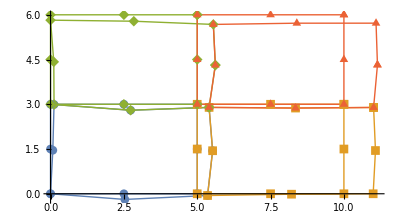

```mathematica
order=2;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\prob1p2els.txt","Table"],1];
t=topol;
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\prob1p2nodes.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=MapThread[Part[#1,#2]&,{allcoords,ord}];
(*or*)
allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]


forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];


(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,10,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,21,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,1}},{0,0}];


(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,21,1,{{1,1},{1,1}},{2400,0}];

(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,20,1,{{1,1},{1,1}},{2400,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,19,1,{{1,1},{1,1}},{2400,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,18,1,{{1,1},{1,1}},{2400,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,17,1,{{1,1},{1,1}},{2400,0}];

Length[KE]
Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

sol=LinearSolve[KE,FE,Method->"Banded"];
Chop[sol]//MatrixForm
scale=500;
deformed=(Flatten[nnodes]+scale sol)

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[defplot,undefplot,PlotRange->All]
```

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{4,7,3,6,2,5,1,8,4}}

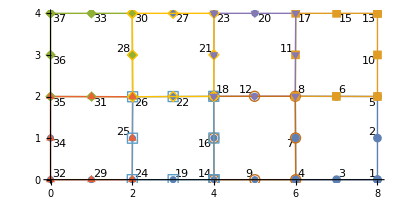

Nnodes = {{8,0},{8,1},{7,0},{6,0},{8,2},{6.99496,2.00285},{5.99496,1.00285},{5.98992,2.0057},{5,0},{8,3},{5.99496,3.00285},{4.99184,2.00478},{8,4},{4,0},{7,4},{3.99688,1.00193},{6,4},{3.99376,2.00386},{3,0},{5,4},{3.99688,3.00193},{3.00112,1.99892},{4,4},{2,0},{2.00424,0.99699},{2.00848,1.99398},{3,4},{2.00424,2.99699},{1,0},{2,4},{1.00424,1.99699},{0,0},{1,4},{0,1},{0,2},{0,3},{0,4}}

Length[nnodes] = 37

sz= 74

aid = {13,17,15}

did = {17,15,13}

aid = {30,37,33}

did = {37,33,30}

aid = {17,23,20}

did = {23,20,17}

aid = {23,30,27}

did = {30,27,23}

vecnodes = {{{6,4},{7,4},{8,4}},{{0,4},{1,4},{2,4}},{{4,4},{5,4},{6,4}},{{2,4},{3,4},{4,4}}}

vecids = {{17,15,13},{37,33,30},{23,20,17},{30,27,23}}

co = {{6,4},{7,4},{8,4}}

vecids[[i]]= {17,15,13}

integralxi1= {31.0436,130.268,33.5875}

vecids[[i,1]] 2 = 34

vecids[[i,2]] 2 = 30

vecids[[i,3]] 2 = 26

vecids[[i,1]]  = 17

co = {{0,4},{1,4},{2,4}}

vecids[[i]]= {37,33,30}

integralxi1= {0.0334591,25.9119,12.8225}

vecids[[i,1]] 2 = 74

vecids[[i,2]] 2 = 66

vecids[[i,3]] 2 = 60

vecids[[i,1]]  = 37

co = {{4,4},{5,4},{6,4}}

vecids[[i]]= {23,20,17}

integralxi1= {23.7736,110.436,31.018}

vecids[[i,1]] 2 = 46

vecids[[i,2]] 2 = 40

vecids[[i,3]] 2 = 34

vecids[[i,1]]  = 23

co = {{2,4},{3,4},{4,4}}

vecids[[i]]= {30,27,23}

integralxi1= {12.8843,73.7908,23.7263}

vecids[[i,1]] 2 = 60

vecids[[i,2]] 2 = 54

vecids[[i,3]] 2 = 46

vecids[[i,1]]  = 30

(0
0
0
0
0
0
0
0
0
0
0.
0
0.
0
0.
0
0
0
0
0
0.
0
0.
0
0
-33.5875
0
0
0.
-130.268
0.
0
0.
-62.0617
0.
0
0
0
0.
-110.436
0.
0
0.
0
0.
-47.4999
0
0
0.
0
0.
0
0.
-73.7908
0.
0
0
0
0.
-25.7068
0.
0
0
0
0.
-25.9119
0.
0
0.
0
0.
0
0.
-0.0334591)

{{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{1,4,7,3,6,2,5,1},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{4,1,5,2,6,3,7,4}}

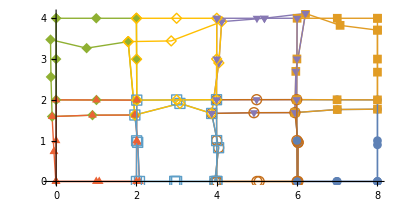

{-41.6431,-102.79,-5.63957}

{-5.50914,-121.103,-6.44246}

{28.6614,14.6429,5.53869}

{-66.1772,-68.2177,-43.2076}

{56.9504,152.856,37.4806}

{-1.63478,-32.5048,-0.928959}

{99.4121,115.555,65.2616}

{29.2698,-166.719,34.8537}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
order=2;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidels-ex1.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidnodes-ex1.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=MapThread[Part[#1,#2]&,{allcoords,ord}];
(*or*)
allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]


forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,32,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,29,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,24,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,19,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,14,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,9,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{1,1},{1,10^12}},{0,0}];
(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,3,0,{{1,1},{1,10^12}},{0,0}];
(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];
(*Dirichlet -  vy=0 no no 2*)


(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,5,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,10,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,13,0,{{10^12,1},{1,1}},{0,0}];


q=100;
L=16;
f[x_]:=q Sin[Pi x/L];
diry=1;
FE=-ContributeLineNewman[FE,f,order,nnodes,topol,37,13,1];
FE//MatrixForm

(*(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,23,1,{{1,1},{1,1}},{0,1000}];*)

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[defplot,undefplot,PlotRange->All]

solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],young,nu][[1]];
stress[[1]]/.{xi->0,eta->0}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}

KE.sol-FE//Chop
```

```mathematica
(*ff[x_]:=a x^2+b x+c
s1=Solve[{ff[0]==1,ff[1]==0,ff[2]==0},{a,b,c}];
s2=Solve[{ff[0]==0,ff[1]==1,ff[2]==0},{a,b,c}];
s3=Solve[{ff[0]==0,ff[1]==0,ff[2]==1},{a,b,c}];
p11=ff[x]/.s1
p12=ff[x]/.s2
p13=ff[x]/.s3
ff[x_]:=a x^2+b x+c
s1=Solve[{ff[2]==1,ff[3]==0,ff[4]==0},{a,b,c}];
s2=Solve[{ff[2]==0,ff[3]==1,ff[4]==0},{a,b,c}];
s3=Solve[{ff[2]==0,ff[3]==0,ff[4]==1},{a,b,c}];
p21=ff[x]/.s1
p22=ff[x]/.s2
p23=ff[x]/.s3
ff[x_]:=a x^2+b x+c
s1=Solve[{ff[4]==1,ff[5]==0,ff[6]==0},{a,b,c}];
s2=Solve[{ff[4]==0,ff[5]==1,ff[6]==0},{a,b,c}];
s3=Solve[{ff[4]==0,ff[5]==0,ff[6]==1},{a,b,c}];
p31=ff[x]/.s1
p32=ff[x]/.s2
p33=ff[x]/.s3
ff[x_]:=a x^2+b x+c
s1=Solve[{ff[6]==1,ff[7]==0,ff[8]==0},{a,b,c}];
s2=Solve[{ff[6]==0,ff[7]==1,ff[8]==0},{a,b,c}];
s3=Solve[{ff[6]==0,ff[7]==0,ff[8]==1},{a,b,c}];
p41=ff[x]/.s1
p42=ff[x]/.s2
p43=ff[x]/.s3
A1=Integrate[p11[[1]] f[x],{x,0,2.}]
B1=Integrate[p12[[1]] f[x],{x,0,2.}]
C1=Integrate[p13[[1]] f[x],{x,0,2.}]
A2=Integrate[p21[[1]] f[x],{x,2,4.}]
B2=Integrate[p22[[1]] f[x],{x,2,4.}]
C2=Integrate[p23[[1]] f[x],{x,2,4.}]
A3=Integrate[p31[[1]] f[x],{x,4,6.}]
B3=Integrate[p32[[1]] f[x],{x,4,6.}]
C3=Integrate[p33[[1]] f[x],{x,4,6.}]
A4=Integrate[p41[[1]] f[x],{x,6,8.}]
B4=Integrate[p42[[1]] f[x],{x,6,8.}]
C4=Integrate[p43[[1]] f[x],{x,6,8.}]
fE=Table[0,{74}];
fE[[13 2]]=C4;
fE[[15 2]]=B4;
fE[[17 2]]=A4+C3;
fE[[20 2]]=B3;
fE[[23 2]]=A3+C2;
fE[[27 2]]=B2;
fE[[30 2]]=A2+C1;
fE[[33 2]]=B1;
fE[[37 2]]=A1;*)
```

{{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2}}

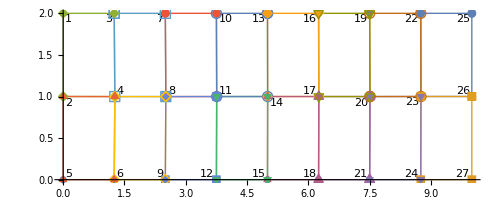

Nnodes = {{0,2},{0,1},{1.25,2},{1.26322,0.999226},{0,0},{1.25,0},{2.5,2},{2.51167,0.999009},{2.5,0},{3.75,2},{3.75658,0.999403},{3.75,0},{5,2},{5.00304,0.999726},{5,0},{6.25,2},{6.25556,0.999501},{6.25,0},{7.5,2},{7.50756,0.999402},{7.5,0},{8.75,2},{8.75501,1.00001},{8.75,0},{10,2},{10,1},{10,0}}

Length[nnodes] = 27

sz= 54

{{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2}}

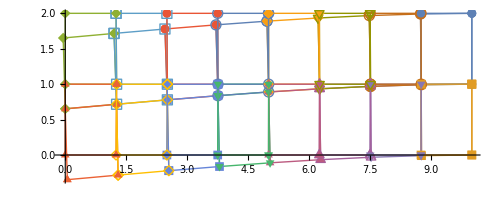

{-881.986,-765.635,-310.039}

{-306.434,-2.864,127.631}

{-501.437,-627.272,154.726}

{1412.92,1667.8,151.564}

{4200.47,4870.82,22.0833}

{-61.8441,33.8735,-314.131}

{4194.82,4866.47,-21.1568}

{4028.45,4659.6,-47.5726}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
order=1;
young=30 10^6;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp1els.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp1nodes.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=MapThread[Part[#1,#2]&,{allcoords,ord}];
(*or*)
allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,27,25,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,1,1,{{1,1},{1,1}},{0,-100}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{0,-100}];
{KE,FE}=ApplyNodeBC[KE,FE,5,1,{{1,1},{1,1}},{0,-100}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=80;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[defplot,undefplot,PlotRange->All]

solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],young,nu][[1]];
stress[[1]]/.{xi->1,eta->1}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}

KE.sol-FE//Chop
```

```mathematica
nnodes
```

{{0,2},{0,1},{1.25,2},{1.26322,0.999226},{0,0},{1.25,0},{2.5,2},{2.51167,0.999009},{2.5,0},{3.75,2},{3.75658,0.999403},{3.75,0},{5,2},{5.00304,0.999726},{5,0},{6.25,2},{6.25556,0.999501},{6.25,0},{7.5,2},{7.50756,0.999402},{7.5,0},{8.75,2},{8.75501,1.00001},{8.75,0},{10,2},{10,1},{10,0}}

```mathematica
allcoords
```

{{{10,1},{10,2},{8.75,2},{8.75501,1.00001}},{{10,0},{10,1},{8.75501,1.00001},{8.75,0}},{{0,2},{0,1},{1.26322,0.999226},{1.25,2}},{{0,1},{0,0},{1.25,0},{1.26322,0.999226}},{{7.5,0},{8.75,0},{8.75501,1.00001},{7.50756,0.999402}},{{7.5,2},{7.50756,0.999402},{8.75501,1.00001},{8.75,2}},{{2.5,2},{1.25,2},{1.26322,0.999226},{2.51167,0.999009}},{{1.26322,0.999226},{1.25,0},{2.5,0},{2.51167,0.999009}},{{6.25,0},{7.5,0},{7.50756,0.999402},{6.25556,0.999501}},{{7.50756,0.999402},{7.5,2},{6.25,2},{6.25556,0.999501}},{{3.75,2},{2.5,2},{2.51167,0.999009},{3.75658,0.999403}},{{2.51167,0.999009},{2.5,0},{3.75,0},{3.75658,0.999403}},{{6.25,2},{5,2},{5.00304,0.999726},{6.25556,0.999501}},{{6.25,0},{6.25556,0.999501},{5.00304,0.999726},{5,0}},{{3.75,0},{5,0},{5.00304,0.999726},{3.75658,0.999403}},{{5.00304,0.999726},{5,2},{3.75,2},{3.75658,0.999403}}}

```mathematica
Min[sol]
```

-0.00435266

```mathematica
stress/.{xi->1,eta->1}
```

{{-881.986,-765.636,-310.039},{-856.059,-672.805,33.692},{4209.99,4931.8,22.735},{4133.79,4787.78,-38.6539},{21.6821,89.8236,253.714},{1088.04,1595.49,33.4272},{13.852,57.3777,-285.22},{3955.98,4645.54,-76.7445},{16.7086,67.3462,289.728},{-2478.47,-2640.3,-229.116},{14.8205,54.3608,-244.645},{3645.79,4331.11,-111.731},{11.5118,47.1903,-151.267},{-3089.69,-3393.03,17.6136},{10.7901,46.8022,331.989},{-3559.88,-3963.13,-149.428}}

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3}}

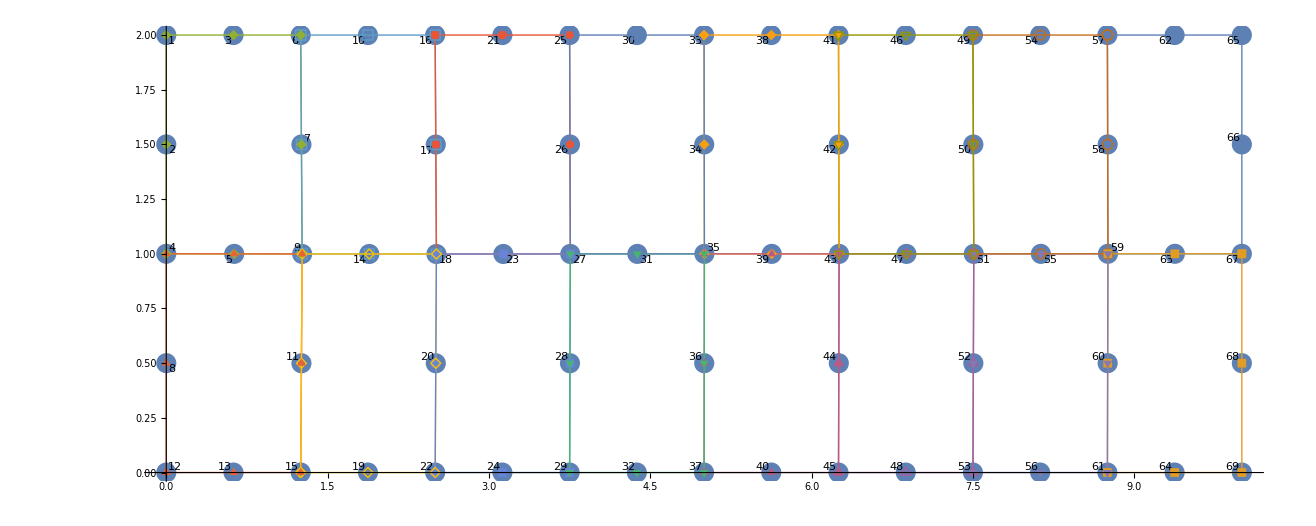

Nnodes = {{0,2},{0,1.5},{0.625,2},{0,1},{0.631611,0.999613},{1.25,2},{1.25661,1.49961},{0,0.5},{1.26322,0.999226},{1.875,2},{1.25661,0.499613},{0,0},{0.625,0},{1.88744,0.999117},{1.25,0},{2.5,2},{2.50583,1.4995},{2.51167,0.999009},{1.875,0},{2.50583,0.499505},{3.125,2},{2.5,0},{3.13412,0.999206},{3.125,0},{3.75,2},{3.75329,1.4997},{3.75658,0.999403},{3.75329,0.499701},{3.75,0},{4.375,2},{4.37981,0.999564},{4.375,0},{5,2},{5.00152,1.49986},{5.00304,0.999726},{5.00152,0.499863},{5,0},{5.625,2},{5.6293,0.999613},{5.625,0},{6.25,2},{6.25278,1.49975},{6.25556,0.999501},{6.25278,0.49975},{6.25,0},{6.875,2},{6.88156,0.999451},{6.875,0},{7.5,2},{7.50378,1.4997},{7.50756,0.999402},{7.50378,0.499701},{7.5,0},{8.125,2},{8.13128,0.999706},{8.125,0},{8.75,2},{8.7525,1.50001},{8.75501,1.00001},{8.7525,0.500005},{8.75,0},{9.375,2},{9.3775,1.00001},{9.375,0},{10,2},{10,1.5},{10,1},{10,0.5},{10,0}}

Length[nnodes] = 69

sz= 138

{{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{1,5,2,6,3,7,4,8,1},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,1,8,4,7,3,6,2,5}}

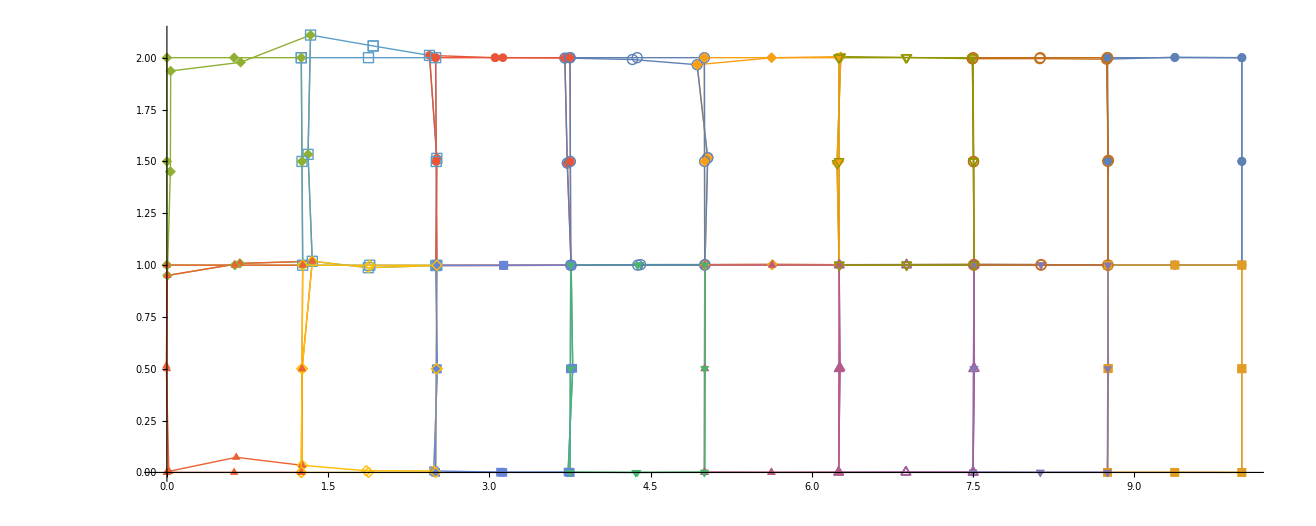

{-37.4197,-27.0679,-18.91}

{-0.750969,0.831368,0.704407}

{-1.45697,0.727722,1.35968}

{5.43954,5.0584,3.12492}

{4.45533,50.2469,12.944}

{21.2966,-34.65,-9.17993}

{-18.6749,-11.7884,16.8537}

{-3.21648,-1.34734,6.79645}

```mathematica
order=2;
young=30 10^6;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp2els.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp2nodes.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];



undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,69,65,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,4,1,{{1,1},{1,1}},{0,-300}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=8000;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[defplot,undefplot,PlotRange->All]

solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],young,nu][[1]];
stress[[1]]/.{xi->1,eta->1}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}
```

```mathematica
Min[sol]
```

-0.0000220195

```mathematica
sol[[65 2]]
```

3.74581×10^-20

```mathematica
FE
```

{0.,0,0.,0,0.,0,0.,-300,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0,0,0,0,0,0,0,0,0,0}